# Mean

```mathematica
iStart=1;
iEnd=10;
SetDirectory[NotebookDirectory[]];
countshA=Import["../data/lattice_v"<>IntegerString[iStart,10,3]<>"/counts/A.txt","Table"];
countshB=Import["../data/lattice_v"<>IntegerString[iStart,10,3]<>"/counts/B.txt","Table"];
countshC=Import["../data/lattice_v"<>IntegerString[iStart,10,3]<>"/counts/C.txt","Table"];
Do[
countshA[[;;,2]]+=Import["../data/lattice_v"<>IntegerString[i,10,3]<>"/counts/A.txt","Table"][[;;,2]];
countshB[[;;,2]]+=Import["../data/lattice_v"<>IntegerString[i,10,3]<>"/counts/B.txt","Table"][[;;,2]];
countshC[[;;,2]]+=Import["../data/lattice_v"<>IntegerString[i,10,3]<>"/counts/C.txt","Table"][[;;,2]];
,{i,iStart+1,iEnd}];
countshA[[;;,2]]/=(iEnd-iStart+1);
countshB[[;;,2]]/=(iEnd-iStart+1);
countshC[[;;,2]]/=(iEnd-iStart+1);
counts=Association[];
counts["A"] =countshA;
counts["B"] =countshB;
counts["C"] =countshC;
```

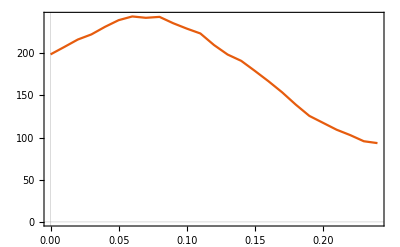

```mathematica
ListLinePlot[counts["A"][[;;25]]]
```

# Variance

```mathematica
iStart=1;
iEnd=300;
SetDirectory[NotebookDirectory[]];
varhA=Import["../data/lattice_v"<>IntegerString[iStart,10,3]<>"/counts/A.txt","Table"];
varhA[[;;,2]]=(varhA[[;;,2]]-countshA[[;;,2]])^2;
Do[
varhA[[;;,2]]+=(Import["../data/lattice_v"<>IntegerString[i,10,3]<>"/counts/A.txt","Table"][[;;,2]]-countshA[[;;,2]])^2;
,{i,iStart+1,iEnd}];
varhA[[;;,2]]/=(iEnd-iStart+1);
stdhA=varhA;
stdhA[[;;,2]]=Sqrt[stdhA[[;;,2]]];
```

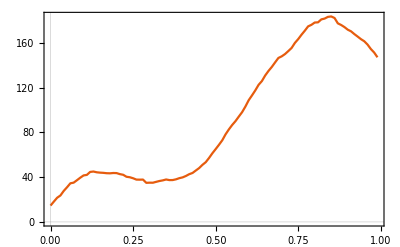

```mathematica
ListLinePlot[stdhA[[;;100]]]
```

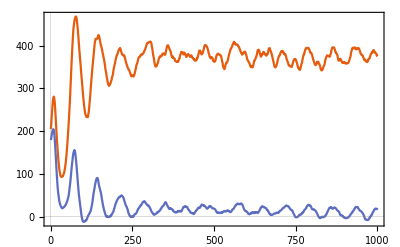

```mathematica
ListLinePlot[{countshA[[;;,2]]+stdhA[[;;,2]]//N,countshA[[;;,2]]-stdhA[[;;,2]]//N}]
```

# Subsample

```mathematica
sampleSize=100;
SetDirectory[NotebookDirectory[]];
countshAs=Import["../data/lattice_v"<>IntegerString[RandomChoice[Range[1,300]],10,3]<>"/counts/A.txt","Table"];
Do[
countshAs[[;;,2]]+=Import["../data/lattice_v"<>IntegerString[RandomChoice[Range[1,300]],10,3]<>"/counts/A.txt","Table"][[;;,2]];
,{i,2,sampleSize}];
countshAs[[;;,2]]/=sampleSize;
```

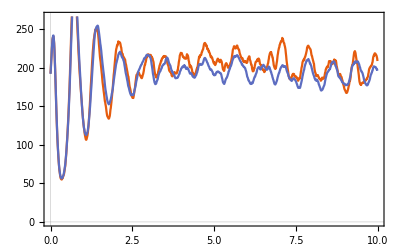

```mathematica
ListLinePlot[{countshAs,countshA}]
```